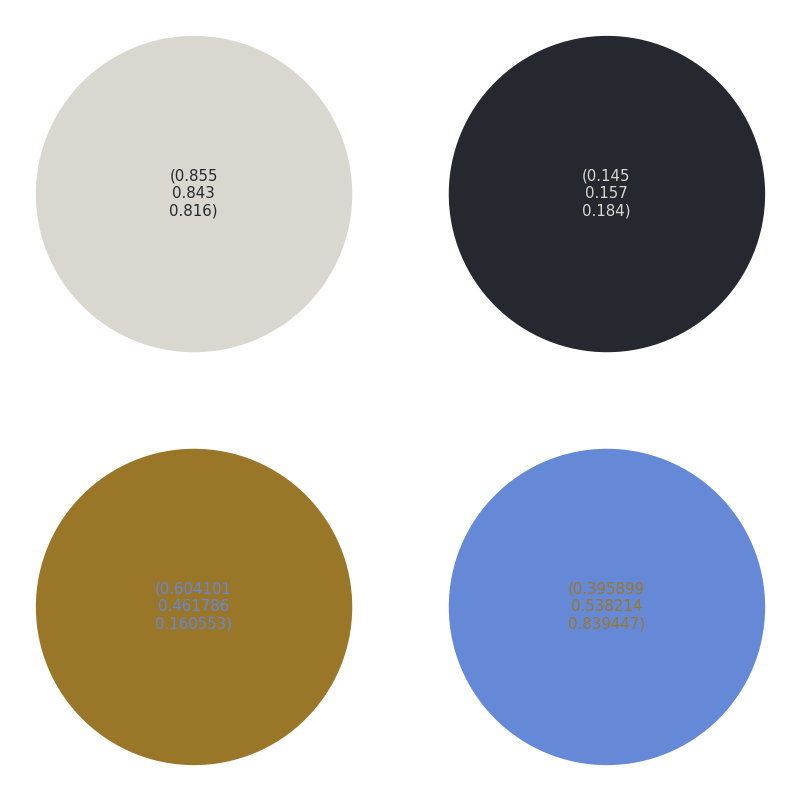

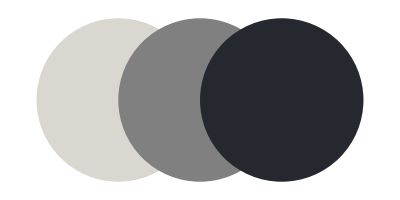

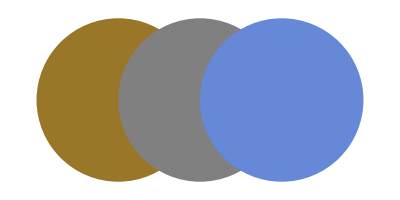

```mathematica
w=RandomReal[];
x=RandomReal[];
y=RandomReal[];
(*Case 1*)
red1=RandomReal[];grn1=RandomReal[];blu1=RandomReal[];
(*red1=N[0.855];grn1=N[0.843];blu1=N[0.816];*)
Color1=RGBColor[red1,grn1,blu1];
Color1Complement=RGBColor[1-red1,1-grn1,1-blu1];
(*Case 2*)
red2=RandomReal[];grn2=RandomReal[];blu2=RandomReal[];
Color2=RGBColor[red2,grn2,blu2];
Color2Complement=RGBColor[1-red2,1-grn2,1-blu2];
(*Matrix of RGB Values*)
Colors={{red1, grn1, blu1}, {red2, grn2, blu2}, {w, x, y}};ColorsComplement={{1-red1, 1-grn1, 1-blu1}, {1-red2, 1-grn2, 1-blu2}, {1-w, 1-x, 1-y}};
(*Grays*)
CGray1=RGBColor[Mean[{red1,1-red1}],Mean[{grn1,1-grn1}],Mean[{blu1,1-blu1}]];
CGray2=RGBColor[Mean[{red2,1-red2}],Mean[{grn2,1-grn2}],Mean[{blu2,1-blu2}]];
(*Texts*)
Disk1Text=Text[Style[MatrixForm[Colors[[1]]],Color1Complement,15],{0,0}];
Disk2Text=Text[Style[MatrixForm[ColorsComplement[[1]]],Color1,15],{0,0}];
Disk3Text=Text[Style[MatrixForm[Colors[[2]]],Color2Complement,15],{0,0}];
Disk4Text=Text[Style[MatrixForm[ColorsComplement[[2]]],Color2,15],{0,0}];
(*Grid Components*)
x1=Graphics[{Color1,Disk[],Disk1Text}];
x2=Graphics[{Color1Complement,Disk[],Disk2Text}];
x3=Graphics[{Color2,Disk[],Disk3Text}];
x4=Graphics[{Color2Complement,Disk[],Disk4Text}];
(*Group Components*)
y1=GraphicsGroup[{Color1,Disk[{0,0}],CGray1,Disk[{1,0}],Color1Complement,Disk[{2,0}]}];
y2=GraphicsGroup[{Color2,Disk[{0,0}],CGray2,Disk[{1,0}],Color2Complement,Disk[{2,0}]}];
(*Disks*)
GraphicsGrid[{{x1,x2},{x3,x4}}]
(* Graphics[y1]
Graphics[y2] *)
(*Blend Samples*)
Cz=2;
z1=Graphics[Table[{Blend[{Color1,Color1Complement},x],Disk[{Cz*x,0}]},{x,0,1,1/Cz}]]
z2=Graphics[Table[{Blend[{Color2,Color2Complement},x],Disk[{Cz*x,0}]},{x,0,1,1/Cz}]]
```

```mathematica
query={{a, b, c}, {r, s, t}, {w, x, y}};
query//MatrixForm;
MatrixForm[query[[1]]](*Row 1*)
Transpose[query]//MatrixForm;
MatrixForm[Transpose[query][[1]]](*Column 1*)
```

(a
b
c)

(a
r
w)

```mathematica
Graphics3D[Sphere[
Flatten[Table[{i,j,k},{i,-2,2},{j,-2,2},{k,-2,2}],2],
Flatten[Table[Mod[i+j,2]*(1-(k+2)/4),{i,-2,2},{j,-2,2},{k,-2,2}],2]]]
```

-Graphics3D-

```mathematica
ImageXYZ=-Graphics-;ImageValue[ImageXYZ,{76,75}]
```

{0.854902,0.843137,0.815686}

(«1»)